```mathematica
mati1={{1,1,0,0,0,0},{0,0,0,0,Exp[ⅈ*k1*L],Exp[-ⅈ*k1*L]},{Exp[ⅈ*k1*(L-L2-2d)],Exp[-ⅈ*k1*(L-L2-2d)],-Exp[ⅈ*k2*(L-L2-2d)],-Exp[-ⅈ*k2*(L-L2-2d)],0,0},{0,0,Exp[ⅈ*k2*(L-L2)],Exp[-ⅈ*k2*(L-L2)],-Exp[ⅈ*k1*(L-L2)],-Exp[-ⅈ*k1*(L-L2)]},{k1*Exp[ⅈ*k1*(L-L2-2d)],-k1*Exp[-ⅈ*k1*(L-L2-2d)],-k2*Exp[ⅈ*k2*(L-L2-2d)],k2*Exp[-ⅈ*k2*(L-L2-2d)],0,0},{0,0,k2*Exp[ⅈ*k2*(L-L2)],-k2*Exp[-ⅈ*k2*(L-L2)],-k1*Exp[ⅈ*k1*(L-L2)],k1*Exp[-ⅈ*k1*(L-L2)]}}
```

{{1,1,0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 L),ⅇ^(-ⅈ k1 L)},{ⅇ^(ⅈ k1 (-2 d+L-L2)),ⅇ^(-ⅈ k1 (-2 d+L-L2)),-ⅇ^(ⅈ k2 (-2 d+L-L2)),-ⅇ^(-ⅈ k2 (-2 d+L-L2)),0,0},{0,0,ⅇ^(ⅈ k2 (L-L2)),ⅇ^(-ⅈ k2 (L-L2)),-ⅇ^(ⅈ k1 (L-L2)),-ⅇ^(-ⅈ k1 (L-L2))},{ⅇ^(ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(-ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(ⅈ k2 (-2 d+L-L2)) k2,ⅇ^(-ⅈ k2 (-2 d+L-L2)) k2,0,0},{0,0,ⅇ^(ⅈ k2 (L-L2)) k2,-ⅇ^(-ⅈ k2 (L-L2)) k2,-ⅇ^(ⅈ k1 (L-L2)) k1,ⅇ^(-ⅈ k1 (L-L2)) k1}}

```mathematica
mati12={{1,1,0,0,0,0},{0,0,0,0,Exp[ⅈ*k1*L],Exp[-ⅈ*k1*L]},{Exp[ⅈ*k1*(L-L2-2d)],Exp[-ⅈ*k1*(L-L2-2d)],-Exp[ⅈ*k1*Sqrt[1-r]*(L-L2-2d)],-Exp[-ⅈ*k1*Sqrt[1-r]*(L-L2-2d)],0,0},{0,0,Exp[ⅈ*k1*Sqrt[1-r]*(L-L2)],Exp[-ⅈ*k1*Sqrt[1-r]*(L-L2)],-Exp[ⅈ*k1*(L-L2)],-Exp[-ⅈ*k1*(L-L2)]},{k1*Exp[ⅈ*k1*(L-L2-2d)],-k1*Exp[-ⅈ*k1*(L-L2-2d)],-k1*Sqrt[1-r]*Exp[ⅈ*k1*Sqrt[1-r]*(L-L2-2d)],k1*Sqrt[1-r]*Exp[-ⅈ*k1*Sqrt[1-r]*(L-L2-2d)],0,0},{0,0,k1*Sqrt[1-r]*Exp[ⅈ*k1*Sqrt[1-r]*(L-L2)],-k1*Sqrt[1-r]*Exp[-ⅈ*k1*Sqrt[1-r]*(L-L2)],-k1*Exp[ⅈ*k1*(L-L2)],k1*Exp[-ⅈ*k1*(L-L2)]}}
```

{{1,1,0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 L),ⅇ^(-ⅈ k1 L)},{ⅇ^(ⅈ k1 (-2 d+L-L2)),ⅇ^(-ⅈ k1 (-2 d+L-L2)),-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r)),-ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r)),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r)),ⅇ^(-ⅈ k1 (L-L2) √(1-r)),-ⅇ^(ⅈ k1 (L-L2)),-ⅇ^(-ⅈ k1 (L-L2))},{ⅇ^(ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(-ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r)) k1 √(1-r),ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r)) k1 √(1-r),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r)) k1 √(1-r),-ⅇ^(-ⅈ k1 (L-L2) √(1-r)) k1 √(1-r),-ⅇ^(ⅈ k1 (L-L2)) k1,ⅇ^(-ⅈ k1 (L-L2)) k1}}

```mathematica
mati2={{1,1,0,0,0,0},{0,0,0,0,Exp[ⅈ*k3*L],Exp[-ⅈ*k3*L]},{Exp[ⅈ*k1*(L-L2-2d)],Exp[-ⅈ*k1*(L-L2-2d)],-Exp[ⅈ*k2*(L-L2-2d)],-Exp[-ⅈ*k2*(L-L2-2d)],0,0},{0,0,Exp[ⅈ*k2*(L-L2)],Exp[-ⅈ*k2*(L-L2)],-Exp[ⅈ*k3*(L-L2)],-Exp[-ⅈ*k3*(L-L2)]},{k1*Exp[ⅈ*k1*(L-L2-2d)],-k1*Exp[-ⅈ*k1*(L-L2-2d)],-k2*Exp[ⅈ*k2*(L-L2-2d)],k2*Exp[-ⅈ*k2*(L-L2-2d)],0,0},{0,0,k2*Exp[ⅈ*k2*(L-L2)],-k2*Exp[-ⅈ*k2*(L-L2)],-k3*Exp[ⅈ*k3*(L-L2)],k3*Exp[-ⅈ*k3*(L-L2)]}}
```

{{1,1,0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k3 L),ⅇ^(-ⅈ k3 L)},{ⅇ^(ⅈ k1 (-2 d+L-L2)),ⅇ^(-ⅈ k1 (-2 d+L-L2)),-ⅇ^(ⅈ k2 (-2 d+L-L2)),-ⅇ^(-ⅈ k2 (-2 d+L-L2)),0,0},{0,0,ⅇ^(ⅈ k2 (L-L2)),ⅇ^(-ⅈ k2 (L-L2)),-ⅇ^(ⅈ k3 (L-L2)),-ⅇ^(-ⅈ k3 (L-L2))},{ⅇ^(ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(-ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(ⅈ k2 (-2 d+L-L2)) k2,ⅇ^(-ⅈ k2 (-2 d+L-L2)) k2,0,0},{0,0,ⅇ^(ⅈ k2 (L-L2)) k2,-ⅇ^(-ⅈ k2 (L-L2)) k2,-ⅇ^(ⅈ k3 (L-L2)) k3,ⅇ^(-ⅈ k3 (L-L2)) k3}}

```mathematica
mati22={{1,1,0,0,0,0},{0,0,0,0,Exp[ⅈ*k1*Sqrt[1-r2]*L],Exp[-ⅈ*k1*Sqrt[1-r2]*L]},{Exp[ⅈ*k1*(L-L2-2d)],Exp[-ⅈ*k1*(L-L2-2d)],-Exp[ⅈ*k1*Sqrt[1-r1]*(L-L2-2d)],-Exp[-ⅈ*k1*Sqrt[1-r1]*(L-L2-2d)],0,0},{0,0,Exp[ⅈ*k1*Sqrt[1-r1]*(L-L2)],Exp[-ⅈ*k1*Sqrt[1-r1]*(L-L2)],-Exp[ⅈ*k1*Sqrt[1-r2]*(L-L2)],-Exp[-ⅈ*k1*Sqrt[1-r2]*(L-L2)]},{k1*Exp[ⅈ*k1*(L-L2-2d)],-k1*Exp[-ⅈ*k1*(L-L2-2d)],-k1*Sqrt[1-r1]*Exp[ⅈ*k1*Sqrt[1-r1]*(L-L2-2d)],k1*Sqrt[1-r1]*Exp[-ⅈ*k1*Sqrt[1-r1]*(L-L2-2d)],0,0},{0,0,k1*Sqrt[1-r1]*Exp[ⅈ*k1*Sqrt[1-r1]*(L-L2)],-k1*Sqrt[1-r1]*Exp[-ⅈ*k1*Sqrt[1-r1]*(L-L2)],-k1*Sqrt[1-r2]*Exp[ⅈ*k1*Sqrt[1-r2]*(L-L2)],k1*Sqrt[1-r2]*Exp[-ⅈ*k1*Sqrt[1-r2]*(L-L2)]}}
```

{{1,1,0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 L √(1-r2)),ⅇ^(-ⅈ k1 L √(1-r2))},{ⅇ^(ⅈ k1 (-2 d+L-L2)),ⅇ^(-ⅈ k1 (-2 d+L-L2)),-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1)),-ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1)),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1)),ⅇ^(-ⅈ k1 (L-L2) √(1-r1)),-ⅇ^(ⅈ k1 (L-L2) √(1-r2)),-ⅇ^(-ⅈ k1 (L-L2) √(1-r2))},{ⅇ^(ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(-ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1)) k1 √(1-r1),ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1)) k1 √(1-r1),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1)) k1 √(1-r1),-ⅇ^(-ⅈ k1 (L-L2) √(1-r1)) k1 √(1-r1),-ⅇ^(ⅈ k1 (L-L2) √(1-r2)) k1 √(1-r2),ⅇ^(-ⅈ k1 (L-L2) √(1-r2)) k1 √(1-r2)}}

```mathematica
Det[mati22]
```

ⅇ^(-2 ⅈ k1 (-2 d+L-L2)-2 ⅈ k1 (L-L2) √(1-r1)-2 ⅈ k1 (-2 d+L-L2) √(1-r1)-ⅈ k1 L √(1-r2)-2 ⅈ k1 (L-L2) √(1-r2)) k1^2 (-ⅇ^(ⅈ k1 (L-L2) √(1-r1)+2 ⅈ k1 (L-L2) √(1-r2)) (-ⅇ^(2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √(1-r1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √(1-r1))+ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)) √(1-r1)-ⅇ^(ⅈ k1 (L-L2) √(1-r2)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1))-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)) √(1-r1))-ⅇ^(2 ⅈ k1 L √(1-r2)) (-ⅇ^(ⅈ k1 (L-L2) √(1-r1)) (-ⅇ^(2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √(1-r1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √(1-r1))+ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)) √(1-r1)-ⅇ^(ⅈ k1 (L-L2) √(1-r2)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1))-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)) √(1-r1))+ⅇ^(ⅈ k1 (L-L2) √(1-r1)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2))+ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2))+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2))+ⅇ^(ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) √(1-r1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) √(1-r1)+ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) √(1-r1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) √(1-r1)) √(1-r2))-ⅇ^(ⅈ k1 (L-L2) √(1-r1)+2 ⅈ k1 (L-L2) √(1-r2)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2))+ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2))+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2))+ⅇ^(ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) √(1-r1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) √(1-r1)+ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) √(1-r1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)+ⅈ k1 (L-L2) √(1-r2)) √(1-r1)) √(1-r2))

```mathematica
Simplify[%7]
```

ⅇ^(ⅈ k1 (-7+2 d (1+√(1-r1))-4 √(1-r1))) k1^2 (ⅇ^(2 ⅈ k1 (5-2 d+2 √(1-r1))) (2+2 √(1-r1)-r1)+ⅇ^(4 ⅈ k1 (2-d+√(1-r1))) r1+ⅇ^(2 ⅈ k1 (3+2 √(1-r1))) r1-ⅇ^(2 ⅈ k1 (3-2 (-1+d) √(1-r1))) r1-ⅇ^(-4 ⅈ k1 (-2+d-√(1-r1)+d √(1-r1))) r1+ⅇ^(2 ⅈ k1 (2-2 (-1+d) √(1-r1))) (-2 (1+√(1-r1))+r1)-ⅇ^(4 ⅈ k1 (1+√(1-r1))) (-2+2 √(1-r1)+r1)+ⅇ^(2 ⅈ k1 (5-2 d-2 (-1+d) √(1-r1))) (-2+2 √(1-r1)+r1))

```mathematica
Det[mati12]
```

ⅇ^(-ⅈ k1 L-2 ⅈ k1 (L-L2)-2 ⅈ k1 (-2 d+L-L2)-2 ⅈ k1 (L-L2) √(1-r)-2 ⅈ k1 (-2 d+L-L2) √(1-r)) k1^2 (2 ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r)+ⅈ k1 (-2 d+L-L2) √(1-r))+2 ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r)+ⅈ k1 (-2 d+L-L2) √(1-r))-2 ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r)+3 ⅈ k1 (-2 d+L-L2) √(1-r))-2 ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r)+3 ⅈ k1 (-2 d+L-L2) √(1-r))-2 ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r)+ⅈ k1 (-2 d+L-L2) √(1-r)) √(1-r)+2 ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r)+ⅈ k1 (-2 d+L-L2) √(1-r)) √(1-r)-2 ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r)+3 ⅈ k1 (-2 d+L-L2) √(1-r)) √(1-r)+2 ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r)+3 ⅈ k1 (-2 d+L-L2) √(1-r)) √(1-r)+ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r)+ⅈ k1 (-2 d+L-L2) √(1-r)) r-ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r)+ⅈ k1 (-2 d+L-L2) √(1-r)) r-ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r)+ⅈ k1 (-2 d+L-L2) √(1-r)) r+ⅇ^(3 ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r)+ⅈ k1 (-2 d+L-L2) √(1-r)) r-ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r)+3 ⅈ k1 (-2 d+L-L2) √(1-r)) r+ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r)+3 ⅈ k1 (-2 d+L-L2) √(1-r)) r+ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r)+3 ⅈ k1 (-2 d+L-L2) √(1-r)) r-ⅇ^(3 ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r)+3 ⅈ k1 (-2 d+L-L2) √(1-r)) r)

```mathematica
Simplify[%10]
```

{{1,1,0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 L),ⅇ^(-ⅈ k1 L)},{ⅇ^(-ⅈ k1 (2 d-L+L2)),ⅇ^(ⅈ k1 (2 d-L+L2)),-ⅇ^(-ⅈ k1 (2 d-L+L2) √(1-r)),-ⅇ^(ⅈ k1 (2 d-L+L2) √(1-r)),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r)),ⅇ^(-ⅈ k1 (L-L2) √(1-r)),-ⅇ^(ⅈ k1 (L-L2)),-ⅇ^(-ⅈ k1 (L-L2))},{ⅇ^(-ⅈ k1 (2 d-L+L2)) k1,-ⅇ^(ⅈ k1 (2 d-L+L2)) k1,-ⅇ^(-ⅈ k1 (2 d-L+L2) √(1-r)) k1 √(1-r),ⅇ^(ⅈ k1 (2 d-L+L2) √(1-r)) k1 √(1-r),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r)) k1 √(1-r),-ⅇ^(-ⅈ k1 (L-L2) √(1-r)) k1 √(1-r),-ⅇ^(ⅈ k1 (L-L2)) k1,ⅇ^(-ⅈ k1 (L-L2)) k1}}

```mathematica
fed[k1_,L_,L2_,d_,r_]:=-ⅇ^(ⅈ k1 (L-2 L2+2d (-1+√(1-r)))) k1^2 (ⅇ^(-2 ⅈ k1 (L-L2+2 d (-1+√(1-r)))) (2+2 √(1-r)-r)-r-ⅇ^(2 ⅈ k1 (2 d-L+2 L2)) r+ⅇ^(-2 ⅈ k1 (L-2 L2+2 d (-1+√(1-r)))) r+ⅇ^(-4 ⅈ d k1 √(1-r)) r+ⅇ^(2 ⅈ k1 L2) (-2 (1+√(1-r))+r)+ⅇ^(2 ⅈ k1 (2 d-L+L2)) (-2+2 √(1-r)+r)-ⅇ^(2 ⅈ k1 (L2-2 d √(1-r))) (-2+2 √(1-r)+r))
```

```mathematica
fed2[k1_,L_,L2_,d_,r1_,r2_]:=ⅇ^(ⅈ k1 (2 d (1+√(1-r1))+L2 (1+2 √(1-r1)+√(1-r2))-L (1+2 √(1-r1)+2 √(1-r2)))) k1^2 (ⅇ^(2 ⅈ k1 ((L-L2) √(1-r1)+L √(1-r2))) (r1-(-1+√(1-r1)) (-1+√(1-r2)))+ⅇ^(2 ⅈ k1 (-2 d (1+√(1-r1))+(L-L2) (1+√(1-r1)+√(1-r2)))) (-r1+(-1+√(1-r1)) (-1+√(1-r2)))+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (1+√(1-r1)+√(1-r2)))) (r1+(1+√(1-r1)) (-1+√(1-r2)))-ⅇ^(2 ⅈ k1 ((-2 d+L-L2) √(1-r1)+L √(1-r2))) (r1+(1+√(1-r1)) (-1+√(1-r2)))-ⅇ^(2 ⅈ k1 (L-L2) (√(1-r1)+√(1-r2))) (r1+(-1+√(1-r1)) (1+√(1-r2)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1)+L √(1-r2))) (r1+(-1+√(1-r1)) (1+√(1-r2)))+ⅇ^(2 ⅈ k1 ((-2 d+L-L2) √(1-r1)+(L-L2) √(1-r2))) (r1-(1+√(1-r1)) (1+√(1-r2)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(L-L2) √(1-r1)+L √(1-r2))) (-r1+(1+√(1-r1)) (1+√(1-r2))))
```

```mathematica
Rootie=FindRoot[fed2[k1,3,1,0.5,1.8,0.0]==0,{k1,4.5}]
```

{k1→5.43443-1.1948×10^-13 ⅈ}

```mathematica
mati221[k1_,L_,L2_,d_,r1_,r2_]:={{1,1,0,0,0,0},{0,0,0,0,Exp[ⅈ*k1*Sqrt[1-r2]*L],Exp[-ⅈ*k1*Sqrt[1-r2]*L]},{Exp[ⅈ*k1*(L-L2-2d)],Exp[-ⅈ*k1*(L-L2-2d)],-Exp[ⅈ*k1*Sqrt[1-r1]*(L-L2-2d)],-Exp[-ⅈ*k1*Sqrt[1-r1]*(L-L2-2d)],0,0},{0,0,Exp[ⅈ*k1*Sqrt[1-r1]*(L-L2)],Exp[-ⅈ*k1*Sqrt[1-r1]*(L-L2)],-Exp[ⅈ*k1*Sqrt[1-r2]*(L-L2)],-Exp[-ⅈ*k1*Sqrt[1-r2]*(L-L2)]},{k1*Exp[ⅈ*k1*(L-L2-2d)],-k1*Exp[-ⅈ*k1*(L-L2-2d)],-k1*Sqrt[1-r1]*Exp[ⅈ*k1*Sqrt[1-r1]*(L-L2-2d)],k1*Sqrt[1-r1]*Exp[-ⅈ*k1*Sqrt[1-r1]*(L-L2-2d)],0,0},{0,0,k1*Sqrt[1-r1]*Exp[ⅈ*k1*Sqrt[1-r1]*(L-L2)],-k1*Sqrt[1-r1]*Exp[-ⅈ*k1*Sqrt[1-r1]*(L-L2)],-k1*Sqrt[1-r2]*Exp[ⅈ*k1*Sqrt[1-r2]*(L-L2)],k1*Sqrt[1-r2]*Exp[-ⅈ*k1*Sqrt[1-r2]*(L-L2)]}}
```

```mathematica
Coefs=Flatten[NullSpace[mati221[k1,3,1,0.5,1.8,0.0]/.Rootie[[1]]]]
```

{0.00519941-0.0000712245 ⅈ,-0.00519941+0.0000712245 ⅈ,-0.0136966-0.999852 ⅈ,-6.36338×10^-9-4.64528×10^-7 ⅈ,0.00426502-0.00297464 ⅈ,-0.0043449-0.0028567 ⅈ}

```mathematica
k11=k1/.Rootie[[1]]
```

5.43443-1.1948×10^-13 ⅈ

```mathematica
ψ[x_,r1_,r2_]:= Piecewise[{{Coefs[[1]]*Exp[ⅈ*k11*x]+Coefs[[2]]*Exp[-ⅈ*k11*x],0<=x<1.0},{Coefs[[3]]*Exp[ⅈ*k11*Sqrt[1-r1]*x]+Coefs[[4]]*Exp[-ⅈ*k11*Sqrt[1-r1]*x],1.0<=x<2.0},{Coefs[[5]]*Exp[ⅈ*k11*Sqrt[1-r2]*x]+Coefs[[6]]*Exp[-ⅈ*k11*Sqrt[1-r2]*x],2.0<=x<3}}]
```

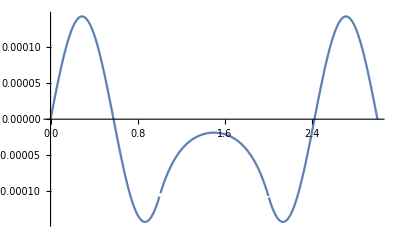

```mathematica
Plot[Re[ψ[x,1.8,0.0]],{x,0,3},PlotRange->Full]
```

```mathematica
fed39[k1_,L_,L2_,d_,r1_,r2_]:=ⅇ^(ⅈ k1 (2 d (1+√(1-r1))+L2 (1+2 √(1-r1)+√(1-r2))-L (1+2 √(1-r1)+2 √(1-r2)))) k1^2 (ⅇ^(2 ⅈ k1 ((L-L2) √(1-r1)+L √(1-r2))) (r1-(-1+√(1-r1)) (-1+√(1-r2)))+ⅇ^(2 ⅈ k1 (-2 d (1+√(1-r1))+(L-L2) (1+√(1-r1)+√(1-r2)))) (-r1+(-1+√(1-r1)) (-1+√(1-r2)))+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (1+√(1-r1)+√(1-r2)))) (r1+(1+√(1-r1)) (-1+√(1-r2)))-ⅇ^(2 ⅈ k1 ((-2 d+L-L2) √(1-r1)+L √(1-r2))) (r1+(1+√(1-r1)) (-1+√(1-r2)))-ⅇ^(2 ⅈ k1 (L-L2) (√(1-r1)+√(1-r2))) (r1+(-1+√(1-r1)) (1+√(1-r2)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1)+L √(1-r2))) (r1+(-1+√(1-r1)) (1+√(1-r2)))+ⅇ^(2 ⅈ k1 ((-2 d+L-L2) √(1-r1)+(L-L2) √(1-r2))) (r1-(1+√(1-r1)) (1+√(1-r2)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(L-L2) √(1-r1)+L √(1-r2))) (-r1+(1+√(1-r1)) (1+√(1-r2))))
```

```mathematica
fed39[k1,3,1,d,r1,0]
```

ⅇ^(ⅈ k1 (2+2 d (1+√(1-r1))-3 (3+2 √(1-r1))+2 √(1-r1))) k1^2 (ⅇ^(2 ⅈ k1 (5-2 d+2 √(1-r1))) (2 (1+√(1-r1))-r1)+ⅇ^(2 ⅈ k1 (-2 d+2 (2+√(1-r1)))) r1-ⅇ^(2 ⅈ k1 (-2 d (1+√(1-r1))+2 (2+√(1-r1)))) r1+ⅇ^(2 ⅈ k1 (3+2 √(1-r1))) r1-ⅇ^(2 ⅈ k1 (3+(2-2 d) √(1-r1))) r1-ⅇ^(4 ⅈ k1 (1+√(1-r1))) (2 (-1+√(1-r1))+r1)+ⅇ^(2 ⅈ k1 (5-2 d+(2-2 d) √(1-r1))) (2 (-1+√(1-r1))+r1)+ⅇ^(2 ⅈ k1 (2+(2-2 d) √(1-r1))) (-2 (1+√(1-r1))+r1))

```mathematica
Simplify[%6]
```

ⅇ^(ⅈ k1 (-7+2 d (1+√(1-r1))-4 √(1-r1))) k1^2 (ⅇ^(2 ⅈ k1 (5-2 d+2 √(1-r1))) (2+2 √(1-r1)-r1)+ⅇ^(4 ⅈ k1 (2-d+√(1-r1))) r1+ⅇ^(2 ⅈ k1 (3+2 √(1-r1))) r1-ⅇ^(2 ⅈ k1 (3-2 (-1+d) √(1-r1))) r1-ⅇ^(-4 ⅈ k1 (-2+d-√(1-r1)+d √(1-r1))) r1+ⅇ^(2 ⅈ k1 (2-2 (-1+d) √(1-r1))) (-2 (1+√(1-r1))+r1)-ⅇ^(4 ⅈ k1 (1+√(1-r1))) (-2+2 √(1-r1)+r1)+ⅇ^(2 ⅈ k1 (5-2 d-2 (-1+d) √(1-r1))) (-2+2 √(1-r1)+r1))

```mathematica
ExpToTrig[%7]
```

k1^2 (-r1 Cos[2 k1 (3-2 (-1+d) √(1-r1))]+r1 Cos[6 k1+4 k1 √(1-r1)]+r1 Cos[8 k1-4 d k1+4 k1 √(1-r1)]-r1 Cos[8 k1-4 d k1+4 k1 √(1-r1)-4 d k1 √(1-r1)]+(-2-2 √(1-r1)+r1) (Cos[2 k1 (2-2 (-1+d) √(1-r1))]+ⅈ Sin[2 k1 (2-2 (-1+d) √(1-r1))])-ⅈ r1 Sin[2 k1 (3-2 (-1+d) √(1-r1))]+(-2+2 √(1-r1)+r1) (Cos[2 k1 (5-2 d-2 (-1+d) √(1-r1))]+ⅈ Sin[2 k1 (5-2 d-2 (-1+d) √(1-r1))])-(-2+2 √(1-r1)+r1) (Cos[4 k1+4 k1 √(1-r1)]+ⅈ Sin[4 k1+4 k1 √(1-r1)])+ⅈ r1 Sin[6 k1+4 k1 √(1-r1)]+ⅈ r1 Sin[8 k1-4 d k1+4 k1 √(1-r1)]+(2+2 √(1-r1)-r1) (Cos[10 k1-4 d k1+4 k1 √(1-r1)]+ⅈ Sin[10 k1-4 d k1+4 k1 √(1-r1)])-ⅈ r1 Sin[8 k1-4 d k1+4 k1 √(1-r1)-4 d k1 √(1-r1)]) (Cos[7 k1-2 d k1+4 k1 √(1-r1)-2 d k1 √(1-r1)]-ⅈ Sin[7 k1-2 d k1+4 k1 √(1-r1)-2 d k1 √(1-r1)])

```mathematica
Simplify[%2]
```

ⅇ^(ⅈ k1 (2 d (1+√(1-r1))+2 L2 (1+√(1-r1))-L (3+2 √(1-r1)))) k1^2 (ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(L-L2) √(1-r1))) (2+2 √(1-r1)-r1)+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (2+√(1-r1)))) r1-ⅇ^(2 ⅈ k1 (-2 d (1+√(1-r1))+(L-L2) (2+√(1-r1)))) r1+ⅇ^(2 ⅈ k1 (L+(L-L2) √(1-r1))) r1-ⅇ^(2 ⅈ k1 (L+(-2 d+L-L2) √(1-r1))) r1+ⅇ^(2 ⅈ k1 (L-L2+(-2 d+L-L2) √(1-r1))) (-2 (1+√(1-r1))+r1)-ⅇ^(2 ⅈ k1 (L-L2) (1+√(1-r1))) (-2+2 √(1-r1)+r1)+ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(-2 d+L-L2) √(1-r1))) (-2+2 √(1-r1)+r1))

```mathematica
ExpToTrig[%3]
```

k1^2 (Cos[2 d k1-3 k1 L+2 k1 L2+2 d k1 √(1-r1)-2 k1 L √(1-r1)+2 k1 L2 √(1-r1)]+ⅈ Sin[2 d k1-3 k1 L+2 k1 L2+2 d k1 √(1-r1)-2 k1 L √(1-r1)+2 k1 L2 √(1-r1)]) (r1 Cos[2 k1 (-2 d+(L-L2) (2+√(1-r1)))]+r1 Cos[2 k1 (L+(L-L2) √(1-r1))]-r1 Cos[2 k1 (L+(-2 d+L-L2) √(1-r1))]-r1 Cos[4 d k1-4 k1 L+4 k1 L2+4 d k1 √(1-r1)-2 k1 L √(1-r1)+2 k1 L2 √(1-r1)]+ⅈ r1 Sin[2 k1 (-2 d+(L-L2) (2+√(1-r1)))]-(-2+2 √(1-r1)+r1) (Cos[2 k1 (L-L2) (1+√(1-r1))]+ⅈ Sin[2 k1 (L-L2) (1+√(1-r1))])+ⅈ r1 Sin[2 k1 (L+(L-L2) √(1-r1))]-ⅈ r1 Sin[2 k1 (L+(-2 d+L-L2) √(1-r1))]+(-2-2 √(1-r1)+r1) (Cos[2 k1 (L-L2+(-2 d+L-L2) √(1-r1))]+ⅈ Sin[2 k1 (L-L2+(-2 d+L-L2) √(1-r1))])+(-2+2 √(1-r1)+r1) (Cos[2 k1 (-2 d+2 L-L2+(-2 d+L-L2) √(1-r1))]+ⅈ Sin[2 k1 (-2 d+2 L-L2+(-2 d+L-L2) √(1-r1))])+(2+2 √(1-r1)-r1) (Cos[4 d k1-4 k1 L+2 k1 L2-2 k1 L √(1-r1)+2 k1 L2 √(1-r1)]-ⅈ Sin[4 d k1-4 k1 L+2 k1 L2-2 k1 L √(1-r1)+2 k1 L2 √(1-r1)])+ⅈ r1 Sin[4 d k1-4 k1 L+4 k1 L2+4 d k1 √(1-r1)-2 k1 L √(1-r1)+2 k1 L2 √(1-r1)])

```mathematica
k1,3,1,0.5,0.8
```

```mathematica
fed89[k1_,d_,r1]:=k1^2 (-r1 Cos[2 k1 (3-2 (-1+d) √(1-r1))]+r1 Cos[6 k1+4 k1 √(1-r1)]+r1 Cos[8 k1-4 d k1+4 k1 √(1-r1)]-r1 Cos[8 k1-4 d k1+4 k1 √(1-r1)-4 d k1 √(1-r1)]+(-2-2 √(1-r1)+r1) (Cos[2 k1 (2-2 (-1+d) √(1-r1))]+ⅈ Sin[2 k1 (2-2 (-1+d) √(1-r1))])-ⅈ r1 Sin[2 k1 (3-2 (-1+d) √(1-r1))]+(-2+2 √(1-r1)+r1) (Cos[2 k1 (5-2 d-2 (-1+d) √(1-r1))]+ⅈ Sin[2 k1 (5-2 d-2 (-1+d) √(1-r1))])-(-2+2 √(1-r1)+r1) (Cos[4 k1+4 k1 √(1-r1)]+ⅈ Sin[4 k1+4 k1 √(1-r1)])+ⅈ r1 Sin[6 k1+4 k1 √(1-r1)]+ⅈ r1 Sin[8 k1-4 d k1+4 k1 √(1-r1)]+(2+2 √(1-r1)-r1) (Cos[10 k1-4 d k1+4 k1 √(1-r1)]+ⅈ Sin[10 k1-4 d k1+4 k1 √(1-r1)])-ⅈ r1 Sin[8 k1-4 d k1+4 k1 √(1-r1)-4 d k1 √(1-r1)]) (Cos[7 k1-2 d k1+4 k1 √(1-r1)-2 d k1 √(1-r1)]-ⅈ Sin[7 k1-2 d k1+4 k1 √(1-r1)-2 d k1 √(1-r1)])
```

```mathematica
mati221[k1,L,L2,d,r1,0]
```

{{1,1,0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 L),ⅇ^(-ⅈ k1 L)},{ⅇ^(ⅈ k1 (-2 d+L-L2)),ⅇ^(-ⅈ k1 (-2 d+L-L2)),-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1)),-ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1)),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1)),ⅇ^(-ⅈ k1 (L-L2) √(1-r1)),-ⅇ^(ⅈ k1 (L-L2)),-ⅇ^(-ⅈ k1 (L-L2))},{ⅇ^(ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(-ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1)) k1 √(1-r1),ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1)) k1 √(1-r1),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1)) k1 √(1-r1),-ⅇ^(-ⅈ k1 (L-L2) √(1-r1)) k1 √(1-r1),-ⅇ^(ⅈ k1 (L-L2)) k1,ⅇ^(-ⅈ k1 (L-L2)) k1}}

```mathematica
Det[%141]
```

ⅇ^(-ⅈ k1 L-2 ⅈ k1 (L-L2)-2 ⅈ k1 (-2 d+L-L2)-2 ⅈ k1 (L-L2) √(1-r1)-2 ⅈ k1 (-2 d+L-L2) √(1-r1)) k1^2 (2 ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1))+2 ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1))-2 ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r1)+3 ⅈ k1 (-2 d+L-L2) √(1-r1))-2 ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r1)+3 ⅈ k1 (-2 d+L-L2) √(1-r1))-2 ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)+2 ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)-2 ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r1)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)+2 ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r1)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)+ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)) r1-ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)) r1-ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)) r1+ⅇ^(3 ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (L-L2) √(1-r1)+ⅈ k1 (-2 d+L-L2) √(1-r1)) r1-ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r1)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) r1+ⅇ^(3 ⅈ k1 (L-L2)+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r1)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) r1+ⅇ^(2 ⅈ k1 L+ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r1)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) r1-ⅇ^(3 ⅈ k1 (L-L2)+3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (L-L2) √(1-r1)+3 ⅈ k1 (-2 d+L-L2) √(1-r1)) r1)

```mathematica
Cancel[%142]
```

-ⅇ^(-ⅈ k1 L-ⅈ k1 (L-L2)-ⅈ k1 (-2 d+L-L2)-ⅈ k1 (L-L2) √(1-r1)-ⅈ k1 (-2 d+L-L2) √(1-r1)) k1^2 (-2 ⅇ^(2 ⅈ k1 (L-L2)+2 ⅈ k1 (L-L2) √(1-r1))-2 ⅇ^(2 ⅈ k1 L+2 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1))+2 ⅇ^(2 ⅈ k1 (L-L2)+2 ⅈ k1 (-2 d+L-L2) √(1-r1))+2 ⅇ^(2 ⅈ k1 L+2 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (-2 d+L-L2) √(1-r1))+2 ⅇ^(2 ⅈ k1 (L-L2)+2 ⅈ k1 (L-L2) √(1-r1)) √(1-r1)-2 ⅇ^(2 ⅈ k1 L+2 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)) √(1-r1)+2 ⅇ^(2 ⅈ k1 (L-L2)+2 ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)-2 ⅇ^(2 ⅈ k1 L+2 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (-2 d+L-L2) √(1-r1)) √(1-r1)-ⅇ^(2 ⅈ k1 L+2 ⅈ k1 (L-L2) √(1-r1)) r1+ⅇ^(2 ⅈ k1 (L-L2)+2 ⅈ k1 (L-L2) √(1-r1)) r1+ⅇ^(2 ⅈ k1 L+2 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)) r1-ⅇ^(2 ⅈ k1 (L-L2)+2 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (L-L2) √(1-r1)) r1+ⅇ^(2 ⅈ k1 L+2 ⅈ k1 (-2 d+L-L2) √(1-r1)) r1-ⅇ^(2 ⅈ k1 (L-L2)+2 ⅈ k1 (-2 d+L-L2) √(1-r1)) r1-ⅇ^(2 ⅈ k1 L+2 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (-2 d+L-L2) √(1-r1)) r1+ⅇ^(2 ⅈ k1 (L-L2)+2 ⅈ k1 (-2 d+L-L2)+2 ⅈ k1 (-2 d+L-L2) √(1-r1)) r1)

```mathematica
Simplify[%143]
```

-ⅇ^(ⅈ k1 (L-2 L2+2 d (-1+√(1-r1)))) k1^2 (ⅇ^(-2 ⅈ k1 (L-L2+2 d (-1+√(1-r1)))) (2+2 √(1-r1)-r1)-r1-ⅇ^(2 ⅈ k1 (2 d-L+2 L2)) r1+ⅇ^(-2 ⅈ k1 (L-2 L2+2 d (-1+√(1-r1)))) r1+ⅇ^(-4 ⅈ d k1 √(1-r1)) r1+ⅇ^(2 ⅈ k1 L2) (-2 (1+√(1-r1))+r1)+ⅇ^(2 ⅈ k1 (2 d-L+L2)) (-2+2 √(1-r1)+r1)-ⅇ^(2 ⅈ k1 (L2-2 d √(1-r1))) (-2+2 √(1-r1)+r1))

```mathematica
ExpToTrig[%144]
```

-k1^2 (Cos[2 d k1-k1 L+2 k1 L2-2 d k1 √(1-r1)]-ⅈ Sin[2 d k1-k1 L+2 k1 L2-2 d k1 √(1-r1)]) (-r1-r1 Cos[4 d k1-2 k1 L+4 k1 L2]+r1 Cos[4 d k1-2 k1 L+4 k1 L2-4 d k1 √(1-r1)]+r1 Cos[4 d k1 √(1-r1)]+(-2-2 √(1-r1)+r1) (Cos[2 k1 L2]+ⅈ Sin[2 k1 L2])+(-2+2 √(1-r1)+r1) (Cos[2 k1 (2 d-L+L2)]+ⅈ Sin[2 k1 (2 d-L+L2)])-ⅈ r1 Sin[4 d k1-2 k1 L+4 k1 L2]-(-2+2 √(1-r1)+r1) (Cos[2 k1 L2-4 d k1 √(1-r1)]+ⅈ Sin[2 k1 L2-4 d k1 √(1-r1)])+(2+2 √(1-r1)-r1) (Cos[4 d k1-2 k1 L+2 k1 L2-4 d k1 √(1-r1)]+ⅈ Sin[4 d k1-2 k1 L+2 k1 L2-4 d k1 √(1-r1)])+ⅈ r1 Sin[4 d k1-2 k1 L+4 k1 L2-4 d k1 √(1-r1)]-ⅈ r1 Sin[4 d k1 √(1-r1)])

```mathematica
Simplify[%145]
```

-k1^2 (Cos[k1 (L-2 L2+2 d (-1+√(1-r1)))]+ⅈ Sin[k1 (L-2 L2+2 d (-1+√(1-r1)))]) (-r1-r1 Cos[2 k1 (2 d-L+2 L2)]+r1 Cos[2 k1 (L-2 L2+2 d (-1+√(1-r1)))]+r1 Cos[4 d k1 √(1-r1)]+(-2 (1+√(1-r1))+r1) (Cos[2 k1 L2]+ⅈ Sin[2 k1 L2])+(-2+2 √(1-r1)+r1) (Cos[2 k1 (2 d-L+L2)]+ⅈ Sin[2 k1 (2 d-L+L2)])-ⅈ r1 Sin[2 k1 (2 d-L+2 L2)]+(2+2 √(1-r1)-r1) (Cos[2 k1 (-L+L2-2 d (-1+√(1-r1)))]+ⅈ Sin[2 k1 (-L+L2-2 d (-1+√(1-r1)))])-ⅈ r1 Sin[2 k1 (L-2 L2+2 d (-1+√(1-r1)))]-(-2+2 √(1-r1)+r1) (Cos[2 k1 (L2-2 d √(1-r1))]+ⅈ Sin[2 k1 (L2-2 d √(1-r1))])-ⅈ r1 Sin[4 d k1 √(1-r1)])

```mathematica
mati222[k1_,d_,r1_]:=mati221[k1,3,1,d,r1,0]
```

```mathematica
mati222[k1,d,r1]
```

{{1,1,0,0,0,0},{0,0,0,0,ⅇ^(3 ⅈ k1),ⅇ^(-3 ⅈ k1)},{ⅇ^(ⅈ (2-2 d) k1),ⅇ^(-ⅈ (2-2 d) k1),-ⅇ^(ⅈ (2-2 d) k1 √(1-r1)),-ⅇ^(-ⅈ (2-2 d) k1 √(1-r1)),0,0},{0,0,ⅇ^(2 ⅈ k1 √(1-r1)),ⅇ^(-2 ⅈ k1 √(1-r1)),-ⅇ^(2 ⅈ k1),-ⅇ^(-2 ⅈ k1)},{ⅇ^(ⅈ (2-2 d) k1) k1,-ⅇ^(-ⅈ (2-2 d) k1) k1,-ⅇ^(ⅈ (2-2 d) k1 √(1-r1)) k1 √(1-r1),ⅇ^(-ⅈ (2-2 d) k1 √(1-r1)) k1 √(1-r1),0,0},{0,0,ⅇ^(2 ⅈ k1 √(1-r1)) k1 √(1-r1),-ⅇ^(-2 ⅈ k1 √(1-r1)) k1 √(1-r1),-ⅇ^(2 ⅈ k1) k1,ⅇ^(-2 ⅈ k1) k1}}

```mathematica
Det[%41]
```

ⅇ^(-7 ⅈ k1-2 ⅈ (2-2 d) k1-4 ⅈ k1 √(1-r1)-2 ⅈ (2-2 d) k1 √(1-r1)) k1^2 (2 ⅇ^(6 ⅈ k1+ⅈ (2-2 d) k1+6 ⅈ k1 √(1-r1)+ⅈ (2-2 d) k1 √(1-r1))+2 ⅇ^(8 ⅈ k1+3 ⅈ (2-2 d) k1+6 ⅈ k1 √(1-r1)+ⅈ (2-2 d) k1 √(1-r1))-2 ⅇ^(6 ⅈ k1+ⅈ (2-2 d) k1+2 ⅈ k1 √(1-r1)+3 ⅈ (2-2 d) k1 √(1-r1))-2 ⅇ^(8 ⅈ k1+3 ⅈ (2-2 d) k1+2 ⅈ k1 √(1-r1)+3 ⅈ (2-2 d) k1 √(1-r1))-2 ⅇ^(6 ⅈ k1+ⅈ (2-2 d) k1+6 ⅈ k1 √(1-r1)+ⅈ (2-2 d) k1 √(1-r1)) √(1-r1)+2 ⅇ^(8 ⅈ k1+3 ⅈ (2-2 d) k1+6 ⅈ k1 √(1-r1)+ⅈ (2-2 d) k1 √(1-r1)) √(1-r1)-2 ⅇ^(6 ⅈ k1+ⅈ (2-2 d) k1+2 ⅈ k1 √(1-r1)+3 ⅈ (2-2 d) k1 √(1-r1)) √(1-r1)+2 ⅇ^(8 ⅈ k1+3 ⅈ (2-2 d) k1+2 ⅈ k1 √(1-r1)+3 ⅈ (2-2 d) k1 √(1-r1)) √(1-r1)-ⅇ^(6 ⅈ k1+ⅈ (2-2 d) k1+6 ⅈ k1 √(1-r1)+ⅈ (2-2 d) k1 √(1-r1)) r1+ⅇ^(8 ⅈ k1+ⅈ (2-2 d) k1+6 ⅈ k1 √(1-r1)+ⅈ (2-2 d) k1 √(1-r1)) r1+ⅇ^(6 ⅈ k1+3 ⅈ (2-2 d) k1+6 ⅈ k1 √(1-r1)+ⅈ (2-2 d) k1 √(1-r1)) r1-ⅇ^(8 ⅈ k1+3 ⅈ (2-2 d) k1+6 ⅈ k1 √(1-r1)+ⅈ (2-2 d) k1 √(1-r1)) r1+ⅇ^(6 ⅈ k1+ⅈ (2-2 d) k1+2 ⅈ k1 √(1-r1)+3 ⅈ (2-2 d) k1 √(1-r1)) r1-ⅇ^(8 ⅈ k1+ⅈ (2-2 d) k1+2 ⅈ k1 √(1-r1)+3 ⅈ (2-2 d) k1 √(1-r1)) r1-ⅇ^(6 ⅈ k1+3 ⅈ (2-2 d) k1+2 ⅈ k1 √(1-r1)+3 ⅈ (2-2 d) k1 √(1-r1)) r1+ⅇ^(8 ⅈ k1+3 ⅈ (2-2 d) k1+2 ⅈ k1 √(1-r1)+3 ⅈ (2-2 d) k1 √(1-r1)) r1)

```mathematica
Simplify[%46]
```

ⅇ^(-ⅈ k1 (3+2 d (1+√(1-r1)))) k1^2 (ⅇ^(2 ⅈ k1 (3+2 d √(1-r1))) (2+2 √(1-r1)-r1)-ⅇ^(4 ⅈ k1) r1-ⅇ^(2 ⅈ (k1+2 d k1)) r1+ⅇ^(2 ⅈ k1 (1+2 d (1+√(1-r1)))) r1+ⅇ^(4 ⅈ (k1+d k1 √(1-r1))) r1+ⅇ^(4 ⅈ d k1) (-2 (1+√(1-r1))+r1)+ⅇ^(6 ⅈ k1) (-2+2 √(1-r1)+r1)-ⅇ^(4 ⅈ d k1 (1+√(1-r1))) (-2+2 √(1-r1)+r1))

```mathematica
ExpToTrig[%47]
```

k1^2 (Cos[3 k1+2 d k1+2 d k1 √(1-r1)]-ⅈ Sin[3 k1+2 d k1+2 d k1 √(1-r1)]) (-r1 Cos[4 k1]-r1 Cos[2 k1+4 d k1]+r1 Cos[4 k1+4 d k1 √(1-r1)]+r1 Cos[2 k1+4 d k1+4 d k1 √(1-r1)]-ⅈ r1 Sin[4 k1]+(-2+2 √(1-r1)+r1) (Cos[6 k1]+ⅈ Sin[6 k1])+(-2-2 √(1-r1)+r1) (Cos[4 d k1]+ⅈ Sin[4 d k1])-ⅈ r1 Sin[2 k1+4 d k1]+ⅈ r1 Sin[4 k1+4 d k1 √(1-r1)]+(2+2 √(1-r1)-r1) (Cos[6 k1+4 d k1 √(1-r1)]+ⅈ Sin[6 k1+4 d k1 √(1-r1)])-(-2+2 √(1-r1)+r1) (Cos[4 d k1+4 d k1 √(1-r1)]+ⅈ Sin[4 d k1+4 d k1 √(1-r1)])+ⅈ r1 Sin[2 k1+4 d k1+4 d k1 √(1-r1)])

```mathematica
TrigReduce[%57]
```

-2 ⅈ (k1^2 r1 Sin[k1-2 d k1-2 d k1 √(1-r1)]+2 k1^2 Sin[3 k1-2 d k1-2 d k1 √(1-r1)]-2 k1^2 √(1-r1) Sin[3 k1-2 d k1-2 d k1 √(1-r1)]-k1^2 r1 Sin[3 k1-2 d k1-2 d k1 √(1-r1)]-k1^2 r1 Sin[k1-2 d k1+2 d k1 √(1-r1)]-2 k1^2 Sin[3 k1-2 d k1+2 d k1 √(1-r1)]-2 k1^2 √(1-r1) Sin[3 k1-2 d k1+2 d k1 √(1-r1)]+k1^2 r1 Sin[3 k1-2 d k1+2 d k1 √(1-r1)])

```mathematica
detfun[k1_,d_,r1_]:=ⅇ^(-ⅈ k1 (3+2 d (1+√(1-r1)))) k1^2 (ⅇ^(2 ⅈ k1 (3+2 d √(1-r1))) (2+2 √(1-r1)-r1)-ⅇ^(4 ⅈ k1) r1-ⅇ^(2 ⅈ (k1+2 d k1)) r1+ⅇ^(2 ⅈ k1 (1+2 d (1+√(1-r1)))) r1+ⅇ^(4 ⅈ (k1+d k1 √(1-r1))) r1+ⅇ^(4 ⅈ d k1) (-2 (1+√(1-r1))+r1)+ⅇ^(6 ⅈ k1) (-2+2 √(1-r1)+r1)-ⅇ^(4 ⅈ d k1 (1+√(1-r1))) (-2+2 √(1-r1)+r1))
```

```mathematica
detfun2[k1_,d_,r1_]:=k1^2 (r1 Sin[k1 (1+2 d (-1+√(1-r1)))]+(2+2 √(1-r1)-r1) Sin[k1 (3+2 d (-1+√(1-r1)))]-r1 Sin[k1 (1-2 d (1+√(1-r1)))]-2 Sin[k1 (3-2 d (1+√(1-r1)))]+2 √(1-r1) Sin[k1 (3-2 d (1+√(1-r1)))]+r1 Sin[k1 (3-2 d (1+√(1-r1)))])
```

```mathematica
Plot[Im[detfun2[k1,0.5,1.05]],{k1,0,120},PlotRange->All]
```

-Graphics-

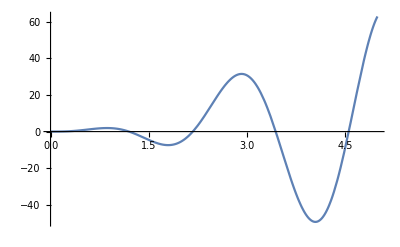

```mathematica
With[{f=Re[detfun2[#,0.5,0.4]]&},solvesol=x/.Solve[{f[x]==0,0≤x≤5},x];
Plot[f[x],{x,0,5},MeshFunctions->{#&},Mesh->{solvesol},MeshStyle->Directive[PointSize[Medium],Red]]]
```

```mathematica
- (k1^2 r1 Sin[k1-2 d k1-2 d k1 √(1-r1)]+2 k1^2 Sin[3 k1-2 d k1-2 d k1 √(1-r1)]-2 k1^2 √(1-r1) Sin[3 k1-2 d k1-2 d k1 √(1-r1)]-k1^2 r1 Sin[3 k1-2 d k1-2 d k1 √(1-r1)]-k1^2 r1 Sin[k1-2 d k1+2 d k1 √(1-r1)]-2 k1^2 Sin[3 k1-2 d k1+2 d k1 √(1-r1)]-2 k1^2 √(1-r1) Sin[3 k1-2 d k1+2 d k1 √(1-r1)]+k1^2 r1 Sin[3 k1-2 d k1+2 d k1 √(1-r1)])
```

-k1^2 r1 Sin[k1-2 d k1-2 d k1 √(1-r1)]-2 k1^2 Sin[3 k1-2 d k1-2 d k1 √(1-r1)]+2 k1^2 √(1-r1) Sin[3 k1-2 d k1-2 d k1 √(1-r1)]+k1^2 r1 Sin[3 k1-2 d k1-2 d k1 √(1-r1)]+k1^2 r1 Sin[k1-2 d k1+2 d k1 √(1-r1)]+2 k1^2 Sin[3 k1-2 d k1+2 d k1 √(1-r1)]+2 k1^2 √(1-r1) Sin[3 k1-2 d k1+2 d k1 √(1-r1)]-k1^2 r1 Sin[3 k1-2 d k1+2 d k1 √(1-r1)]

```mathematica
Simplify[%137]
```

k1^2 (r1 Sin[k1 (1+2 d (-1+√(1-r1)))]+(2+2 √(1-r1)-r1) Sin[k1 (3+2 d (-1+√(1-r1)))]-r1 Sin[k1 (1-2 d (1+√(1-r1)))]-2 Sin[k1 (3-2 d (1+√(1-r1)))]+2 √(1-r1) Sin[k1 (3-2 d (1+√(1-r1)))]+r1 Sin[k1 (3-2 d (1+√(1-r1)))])

```mathematica
detfun[k1_,L_,L2_,d_,r1_]=ⅇ^(-ⅈ k1 (3+2 d (1+√(1-r1)))) k1^2 (ⅇ^(2 ⅈ k1 (3+2 d √(1-r1))) (2+2 √(1-r1)-r1)-ⅇ^(4 ⅈ k1) r1-ⅇ^(2 ⅈ (k1+2 d k1)) r1+ⅇ^(2 ⅈ k1 (1+2 d (1+√(1-r1)))) r1+ⅇ^(4 ⅈ (k1+d k1 √(1-r1))) r1+ⅇ^(4 ⅈ d k1) (-2 (1+√(1-r1))+r1)+ⅇ^(6 ⅈ k1) (-2+2 √(1-r1)+r1)-ⅇ^(4 ⅈ d k1 (1+√(1-r1))) (-2+2 √(1-r1)+r1))
```

ⅇ^(-ⅈ k1 (3+2 d (1+√(1-r1)))) k1^2 (ⅇ^(2 ⅈ k1 (3+2 d √(1-r1))) (2+2 √(1-r1)-r1)-ⅇ^(4 ⅈ k1) r1-ⅇ^(2 ⅈ (k1+2 d k1)) r1+ⅇ^(2 ⅈ k1 (1+2 d (1+√(1-r1)))) r1+ⅇ^(4 ⅈ (k1+d k1 √(1-r1))) r1+ⅇ^(4 ⅈ d k1) (-2 (1+√(1-r1))+r1)+ⅇ^(6 ⅈ k1) (-2+2 √(1-r1)+r1)-ⅇ^(4 ⅈ d k1 (1+√(1-r1))) (-2+2 √(1-r1)+r1))

```mathematica
detfun[k1,L,L/2,d,r1]
```

ⅇ^(-ⅈ k1 (3+2 d (1+√(1-r1)))) k1^2 (ⅇ^(2 ⅈ k1 (3+2 d √(1-r1))) (2+2 √(1-r1)-r1)-ⅇ^(4 ⅈ k1) r1-ⅇ^(2 ⅈ (k1+2 d k1)) r1+ⅇ^(2 ⅈ k1 (1+2 d (1+√(1-r1)))) r1+ⅇ^(4 ⅈ (k1+d k1 √(1-r1))) r1+ⅇ^(4 ⅈ d k1) (-2 (1+√(1-r1))+r1)+ⅇ^(6 ⅈ k1) (-2+2 √(1-r1)+r1)-ⅇ^(4 ⅈ d k1 (1+√(1-r1))) (-2+2 √(1-r1)+r1))

```mathematica
Simplify[%156]
```

ⅇ^(-ⅈ k1 (3+2 d (1+√(1-r1)))) k1^2 (ⅇ^(2 ⅈ k1 (3+2 d √(1-r1))) (2+2 √(1-r1)-r1)-ⅇ^(4 ⅈ k1) r1-ⅇ^(2 ⅈ (k1+2 d k1)) r1+ⅇ^(2 ⅈ k1 (1+2 d (1+√(1-r1)))) r1+ⅇ^(4 ⅈ (k1+d k1 √(1-r1))) r1+ⅇ^(4 ⅈ d k1) (-2 (1+√(1-r1))+r1)+ⅇ^(6 ⅈ k1) (-2+2 √(1-r1)+r1)-ⅇ^(4 ⅈ d k1 (1+√(1-r1))) (-2+2 √(1-r1)+r1))

```mathematica
ExpToTrig[%157]
```

k1^2 (Cos[3 k1+2 d k1+2 d k1 √(1-r1)]-ⅈ Sin[3 k1+2 d k1+2 d k1 √(1-r1)]) (-r1 Cos[4 k1]-r1 Cos[2 k1+4 d k1]+r1 Cos[4 k1+4 d k1 √(1-r1)]+r1 Cos[2 k1+4 d k1+4 d k1 √(1-r1)]-ⅈ r1 Sin[4 k1]+(-2+2 √(1-r1)+r1) (Cos[6 k1]+ⅈ Sin[6 k1])+(-2-2 √(1-r1)+r1) (Cos[4 d k1]+ⅈ Sin[4 d k1])-ⅈ r1 Sin[2 k1+4 d k1]+ⅈ r1 Sin[4 k1+4 d k1 √(1-r1)]+(2+2 √(1-r1)-r1) (Cos[6 k1+4 d k1 √(1-r1)]+ⅈ Sin[6 k1+4 d k1 √(1-r1)])-(-2+2 √(1-r1)+r1) (Cos[4 d k1+4 d k1 √(1-r1)]+ⅈ Sin[4 d k1+4 d k1 √(1-r1)])+ⅈ r1 Sin[2 k1+4 d k1+4 d k1 √(1-r1)])

```mathematica
Simplify[%158]
```

-2 ⅈ k1^2 (-r1 Sin[k1 (1+2 d (-1+√(1-r1)))]+(-2-2 √(1-r1)+r1) Sin[k1 (3+2 d (-1+√(1-r1)))]+r1 Sin[k1 (1-2 d (1+√(1-r1)))]+2 Sin[k1 (3-2 d (1+√(1-r1)))]-2 √(1-r1) Sin[k1 (3-2 d (1+√(1-r1)))]-r1 Sin[k1 (3-2 d (1+√(1-r1)))])

```mathematica
detfun2[k1,1/2,0.25]
```

k1^2 (0.5 Sin[0.866025 k1]-0.0179492 Sin[1.13397 k1]+3.48205 Sin[2.86603 k1])

```mathematica
Manipulate[Plot[{(2 √(1-r1) +r1-2)*Sin[k1 (2-√(1-r1))],(2+2 √(1-r1)-r1) Sin[k1 (2+√(1-r1))],2 r1 Sin[k1 √(1-r1)]},{k1,0,15}],{r1,0,1}]
```

```mathematica
Plot3D[Abs[detfun2[x+ⅈ y,1/2,0.5]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-